\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## BI-BEZ – Bezpečnost – Cvičení 2 Tomáš Zahradnický, Jiří Buček Katedra informační bezpečnosti, FIT ČVUT v Praze

Úvod do software Mathematica (opakování)

Substituční šifra

Afinní šifry

Transpoziční šifra

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Velejemný úvod do software Mathematica

Ve cvičeních bude využíván software Mathematica pro demonstraci šifer, jejich kryptoanalýzy, atd., a proto je důležité se se softwarem Mathematica naučit pracovat alespoň na nějaké základní bázi.

Mathematica je rozdělena na Front End (toto) a Kernel (není vidět). Front End posílá příkazy označené In[cislo] do kernelu a výstup z kernelu je označen Out[cislo]. Příkaz In[cislo] spustíte (pošlete do kernelu k vyhodnocení) pomocí klávesové kombinace SHIFT+ENTER, anebo ENTER na numerické klávesnici.

Před tím, než začneme, Mathematica je case sensitive a velmi dbá na typ závorek a proto pozor. Kulaté závorky označují prioritu vyhodnocování, hranaté určují argumenty funkce a složené označují vektory, matice a seznamy. Více viz dále.

Nyní zkuste vyhodnotit nasledující výrazy:

```mathematica
Mod[283,17]
```

```mathematica
Sin[Pi/2]
```

```mathematica
Sum[1/i^2,{i,1,∞}]
```

```mathematica
Mod[102*BEZInverse[102,113],113]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Inicializace worksheetu

Aby bylo možné použít programy v těchno slajdech, je nutné provést inicializaci. Klepněte kamkoliv do bloku s programem a nechte ho vyhodnotit.  Blok obsahuje definice funkcí, které budou použity pro šifrování, dešifrování a analýzu. Není nutné se těmito funkcemi zaobírat.

```mathematica
<<"BarCharts`";
NCharacters=26;
SYMBOLS=Table[FromCharacterCode[65+i],{i,0,57}];
ENGLISH={0.0805726131341181993`1.9999999999999998,0.0125943599170806117`1.9999999999999998,0.0362576759103531896`1.9999999999999976,0.0380959831032189932`1.9999999999999998,0.1146790784996284273`1.9999999999999998,0.0240935581022411703`1.9999999999999998,0.0157233934368521923`1.9999999999999998,0.031212109359721516`1.9999999999999998,0.0741972073375836039`1.9999999999999998,0.001290726326905777`1.9999999999999998,0.0015254038408886455`1.9999999999999998,0.0429459850588649431`1.9999999999999998,0.0222943638283725115`1.9999999999999998,0.0746274494465521962`1.9999999999999998,0.0873782610396213869`1.9999999999999998,0.0389955802401533226`1.9999999999999998,0.0010169358939257637`1.9999999999999976,0.0751750303125122228`1.9999999999999998,0.0571830875738256346`1.9999999999999998,0.0912504400203387179`1.9999999999999998,0.0322290452536472797`1.9999999999999998,0.0081746000704032542`1.9999999999999998,0.0116165369421519928`1.9999999999999976,0.0017991942738686588`1.9999999999999998,0.0243282356162240388`1.9999999999999998,0.0007431454609457504`1.9999999999999998};
VelikostAbecedy[n_Integer]:=Module[{},NCharacters=n;Take[SYMBOLS,n]]
BEZRotChar[x_,amount_]:=FromCharacterCode[Mod[(ToCharacterCode[x]-ToCharacterCode["A"])+amount,NCharacters]+ToCharacterCode["A"]]
AXPBChar[x_,a_,b_]:=FromCharacterCode[Mod[(ToCharacterCode[x]-ToCharacterCode["A"]) a+b,NCharacters]+ToCharacterCode["A"]]
AXPB::notcoprime="Multiplicativni koefficient je soudelny s modulem. Informace bude ztracena.";
AXPB[x_String,a_,b_]:=Block[{},If[GCD[a,NCharacters]≠1,Message[AXPB::notcoprime]];StringJoin[(AXPBChar[#1,a,b]&)/@Characters[BEZPrepText[x]]]];
AXPBDecrypt[x_String,a_,b_]:=StringJoin[(AXPBCharDecrypt[#1,a,b]&)/@Characters[x]]
BEZZnakPlusB[x_String,b_Integer]:=(BEZRotChar[#1,b]&)/@Characters[x]
AXPBCharDecrypt[x_,a_,b_]:=FromCharacterCode[Mod[((ToCharacterCode[x]-ToCharacterCode["A"])-b) BEZInverse[a,NCharacters],NCharacters]+ToCharacterCode["A"]]
BEZInverse[x_Integer,mod_]:=Inverse[{{x}},Modulus->mod]⟦1⟧⟦1⟧
Caesar[x_String,posun_]:=StringJoin[BEZZnakPlusB[x,posun]]
BEZPrepText[x_String]:=FromCharacterCode[Select[(#1⟦1⟧&)/@ToCharacterCode[Characters[ToUpperCase[x]]],0≤#1-ToCharacterCode["A"]⟦1⟧≤NCharacters&]]
BEZAbsCetnosti[x_String]:=Table[Length[Select[Characters[BEZPrepText[x]],#1===SYMBOLS⟦i⟧&]],{i,1,NCharacters}]
BEZRelCetnosti[x_String]:=N[BEZAbsCetnosti[x]/StringLength[BEZPrepText[x]],2]

RelCetnosti[x_String]:=TableForm[Module[{X},X=BEZRelCetnosti[x];Append[Table[Table[{SYMBOLS⟦7 i+j⟧,X⟦7 i+j⟧},{j,1,7}],{i,0,-1+Floor[NCharacters/7]}],Table[{SYMBOLS⟦7 Floor[NCharacters/7]+i⟧,X⟦7 Floor[NCharacters/7]+i⟧},{i,1,Mod[NCharacters,7]}]]]]
BEZGrafyRelCetnosti[x_String,y_String]:=Module[{RC1,RC2},RC1=BEZRelCetnosti[x];RC2=BEZRelCetnosti[y];BarChart[{RC1,RC2},BarLabels->SYMBOLS,BarEdges->False,BarStyle->{Directive[RGBColor[.1,.2,.7],Opacity[0.7]],Directive[RGBColor[0,.7,0],Opacity[0.7]]},BarSpacing->0.1,Background->GrayLevel[.9]]]
BEZGrafyRelCetnostiSAnglictinou[x_String]:=Module[{RC1,RC2},RC1=BEZRelCetnosti[x];RC2=ENGLISH;BarChart[{RC1,RC2},BarLabels->SYMBOLS,BarEdges->False,BarStyle->{Directive[RGBColor[.1,.2,.7],Opacity[0.7]],Directive[RGBColor[0,.7,0],Opacity[0.7]]},BarSpacing->0.1,Background->GrayLevel[.9]]]
RelCetnostiZBEZRelCetnosti[x_]:=TableForm[{Table[{FromCharacterCode[64+i],x⟦i⟧},{i,7}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,8,14}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,15,21}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,22,26}]}]
Pozice[x_String]:=StringPosition[StringJoin[SYMBOLS],x]⟦1⟧⟦1⟧-1
BEZPadString[x_String,n_Integer]:=If[StringLength[x]<n,BEZPadString[StringJoin[x,"X"],n], If[StringLength[x]==n, x, Abort[]]]
BEZNumToPad[x_String,cols_Integer]:=Floor[(StringLength[x]+cols-1)/cols]*cols
BEZGenerMatrix[x_String,cols_Integer]:=Partition[Characters[BEZPadString[BEZPrepText[x],BEZNumToPad[BEZPrepText[x],cols]]],cols]
Transpozice[x_String,cols_Integer]:=StringJoin[Flatten[Transpose[BEZGenerMatrix[BEZPrepText[x],cols]]]]

Print["Initialization done"]
```

General::obspkg: BarCharts` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Initialization done

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Jednoduché šifry (Caesarova šifra)

Caesarova šifra je známá jako jednoduchá substituční proudová (znaková) šifra, která provádí transformaci y = |x+3|_26. Mějme otevřený text (nechte vyhodnotit)

```mathematica
OT:="ANOPENTEXTTHATWILLGETTRANSFORMEDWITHCAESARCIPHER"
```

Zašifrovaný text bude:

```mathematica
ST=Caesar[OT,3]
```

DQRSHQWHAWWKDWZLOOJHWWUDQVIRUPHGZLWKFDHVDUFLSKHU

Text lze snadno dešifrovat provedením opačné operace (odečtením) posunu:

```mathematica
Caesar[ST,-3]
```

ANOPENTEXTTHATWILLGETTRANSFORMEDWITHCAESARCIPHER

Kryptoanalýzu této šifry naleznete na další stránce.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalýza Caesarovy šifry

Relativní četnosti šifrového textu z minulého slajdu jsou:

```mathematica
RelCetnosti[ST]
```

Relativní četnosti otevřeného textu z minulého slajdu jsou:

```mathematica
RelCetnosti[OT]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalýza Caesarovy šifry (2)

Srovnáním relativních četností (modrá pro šifrový text, zelená pro otevřený text) vidíme, že šifra způsobila posun relativních četností následujícím způsobem:

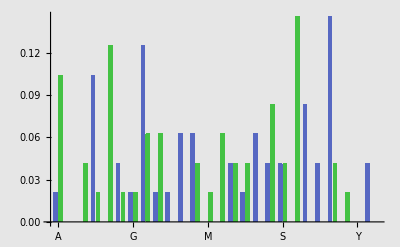

```mathematica
BEZGrafyRelCetnosti[ST,OT]
```

Z grafu vidíme, že pokud známe otevřený text, je velmi snadné uhodnout transformaci, která povede k dešifrování textu. Stačí jen posunout četnosti tak, aby grafy splynuly. Pokud otevřený text k dispozici nemáme, musíme si vystačit například se vzorkem relativních četností pro jazyk, kterým předpokládáme, že je šifrový text psán. Předpokládáme, že šifrový text je psán v angličtině, pro kterou máme relativní četnosti uložené v proměnné ENGLISH.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalýza Caesarovy šifry (3)

Relativní četnosti pro angličtinu jsou (získáno jako relativní četnosti z cca 20 KB souboru):

```mathematica
RelCetnostiZBEZRelCetnosti[ENGLISH]
```

A
0.081 | B
0.013 | C
0.036 | D
0.038 | E
0.11 | F
0.024 | G
0.016
H
0.031 | I
0.074 | J
0.0013 | K
0.0015 | L
0.043 | M
0.022 | N
0.075
O
0.087 | P
0.039 | Q
0.001 | R
0.075 | S
0.057 | T
0.091 | U
0.032
V
0.0082 | W
0.012 | X
0.0018 | Y
0.024 | Z
0.00074 |  |

Nyní můžeme udělat stejný krok, jako v minulém případě a srovnat relativní četnosti šifrového textu s relativními četnostmi pro angličtinu:

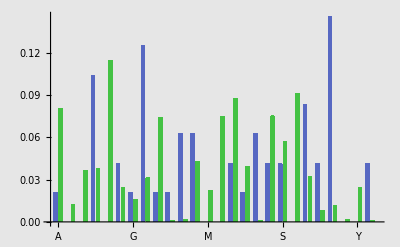

```mathematica
BEZGrafyRelCetnostiSAnglictinou[ST]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Úkol 1: Zjistěte, co se skrývá pod následujícím šifrovým textem

Neznámý šifrový text ST je:

```mathematica
ST="BAGURNGGRZCGAHZOREGUERRABGONQPBATENGHYNGVBAF"
```

BAGURNGGRZCGAHZOREGUERRABGONQPBATENGHYNGVBAF

Proveďte analýzu relativních četností a nalezněte k němu otevřený text. Jde o šifru podobnou Caesarově šifře.

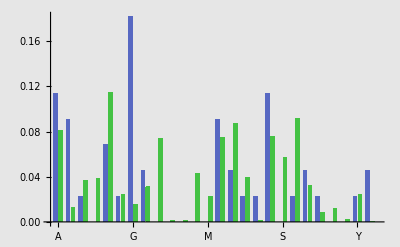

```mathematica
BEZGrafyRelCetnostiSAnglictinou[ST]
```

```mathematica
Caesar[ST,-13]
```

ONTHEATTEMPTNUMBERTHREENOTBADCONGRATULATIONS

Postup: Můžeme porovnat, kde jsou nejmenší četnosti (nebo největší) v zašifrovaném textu a poté se podíváme na nejmenší (největší) četnosti v písmen v angličtině, můžeme si například všimnout, že J a K mají jedny z nejmenších četností, tudíž můžeme zkusit “namapovat J a K na W a X, což odpovída 13x posunu v abecedě. Tedy zkusíme všechny písmena posunout o 13 pozic a to nám dá původní text.”
Návod: Srovnejte relativní četnost. Proměnná ST je globální, takže můžete použít pomůcky uvedené na předchozích slajdech.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Šifry typu |ap+b|_m

Caesarova šifra je speciálním případem afinní šifry |ap+b|_m a je definována jako |p+b|_m. Šifra též představuje substituci, avšak nyní již tato substituce neposunuje graf relativních četností, ale dochází k důkladnějšímu "promíchání" (viz graf relativních četností). Celou věc si ukažme na příkladu:

```mathematica
OT="THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER"
```

THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER

```mathematica
ST=AXPB[OT,5,19]
```

KCHFHFJNKTGLKCNADHQCNAKNEKKCTKZNZHWWNGDHQCNA

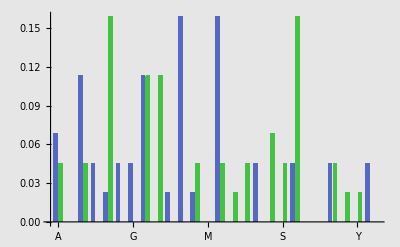

```mathematica
BEZGrafyRelCetnosti[ST,OT]
```

Šifrový text můžeme dešifrovat obrácením šifrovacího předpisu a to je-li y=|ap+b|_mbude p=|a^-1(y-b)|_m.

```mathematica
AXPBDecrypt[ST,5,19]
```

THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER

Můžeme ale využít i původní předpis (formu násobení, sčítání) p=|□ c + □|_m. Jak to dokážeme? Napište obecný výraz (pomocí dosazení). Konkrétně:

```mathematica
AXPB[ST,21,17]
```

THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER

Kolik existuje různých klíčů pro abecedu o m znacích?

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Úkol 2: Kryptoanalýza šifry |ap+b|_m

1. Vyberte náhodné konstanty a a b a s nimi anglický text alespoň o 100 znacích. Takový text můžete nalézt například v libovolné dokumentaci k software. Až budete mít šifrový text, poskytněte ho sousedovi (např. e-mailem), ale nesdělujte mu hodnoty konstant!

```mathematica
OT="‘Yes . , . yes!’ said the Nurse, ‘The rope ladder.’ Her voice was dull. She sat down on a bench and dropped the ladder. She didn’t look at Juliet: she just shook her head slowly and began wringing her hands.

‘Oh dear, ‘ said Juliet ‘What’s wrong? Why are you wringing your hands?’

‘Oh no, oh no,’ said the Nurse, ‘He’s dead, he’s dead, he’s dead. It’s all over – all over, May God help us, he’s gone, he’s killed, he’s dead.’

Juliet went cold. Did she mean Romeo? She was numb, ‘Can heaven be so hostile?’ she said,

‘No,’ said the Nurse. ‘But Romeo can. Oh Romeo, Romeo. Who would have thought it? Romeo!’";
a=9;
b=16;
```

```mathematica
ST=AXPB[OT,a,b]
```

YAWYAWWQKRFBADONWAFBANMVALQRRANBANXMKIAGQWROLLWBAWQFRMGDMDQZADIBQDRRNMVVARFBALQRRANWBARKRDFLMMCQFTOLKAFWBATOWFWBMMCBANBAQRWLMGLYQDRZASQDGNKDSKDSBANBQDRWMBRAQNWQKRTOLKAFGBQFWGNMDSGBYQNAYMOGNKDSKDSYMONBQDRWMBDMMBDMWQKRFBADONWABAWRAQRBAWRAQRBAWRAQRKFWQLLMXANQLLMXANUQYSMRBALVOWBAWSMDABAWCKLLARBAWRAQRTOLKAFGADFIMLRRKRWBAUAQDNMUAMWBAGQWDOUZIQDBAQXADZAWMBMWFKLAWBAWQKRDMWQKRFBADONWAZOFNMUAMIQDMBNMUAMNMUAMGBMGMOLRBQXAFBMOSBFKFNMUAM

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Úkol 2: Kryptoanalýza šifry |ap+b|_m (2)

2. Až obdržíte šifrový text od souseda, přiřaďte jeho hodnotu do proměnné ST:

```mathematica
ST="NAUOMFSFDNALOMFSWLOFAOXNEUFOFJOXLAWSLYEFPLAFEXAFLQOMXATXABXDOMNOJMNOYLOFPLOXLADVLZEUELLDFERSFDFPYEFOMLDFFGWFSXFAJFUYRMZPNADNQOFSNEEOMFRSFOSNXAFULAMZPNAUNONYZOVMNOXQOMFRULAOFAOXSFERUFONJMFUQSLPOMFSFNEVLSEUNAUOMFDFADLSRPNJMXAFSRQLZAUXAMZPNADVMLTALVDVMNONEXFAUFDXSFDOMFRPXBMOJLPFZWVXOM";
```

Nyní proveďte analýzu četnosti:

```mathematica
RelCetnosti[ST]
```

A
0.085 | B
0.0071 | C
0 | D
0.046 | E
0.046 | F
0.13 | G
0.0035
H
0 | I
0 | J
0.021 | K
0 | L
0.078 | M
0.074 | N
0.071
O
0.1 | P
0.035 | Q
0.018 | R
0.028 | S
0.053 | T
0.0071 | U
0.046
V
0.025 | W
0.014 | X
0.06 | Y
0.018 | Z
0.025 |  |

A srovnejte ji s četnostmi pro angličtinu:

```mathematica
RelCetnostiZBEZRelCetnosti[ENGLISH]
```

A
0.081 | B
0.013 | C
0.036 | D
0.038 | E
0.11 | F
0.024 | G
0.016
H
0.031 | I
0.074 | J
0.0013 | K
0.0015 | L
0.043 | M
0.022 | N
0.075
O
0.087 | P
0.039 | Q
0.001 | R
0.075 | S
0.057 | T
0.091 | U
0.032
V
0.0082 | W
0.012 | X
0.0018 | Y
0.024 | Z
0.00074 |  |

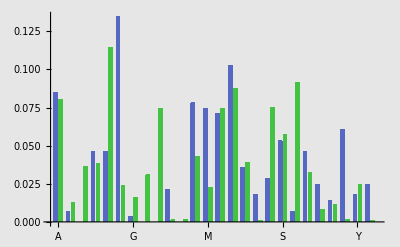

```mathematica
BEZGrafyRelCetnostiSAnglictinou[ST]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Úkol 2: KryptoanalÝza Šifry |ap+b|_m (3)

Z analýzy relativních četností můžeme zjistit, že nejčetnější písmena pro angličtinu jsou E a T. Toho můžeme využít pro zjištění dešifrovacího klíče. Vybereme tedy 2 nejčetnější písmena z analýzy šifrového textu a zkusíme je namapovat na E a T. Řešením soustavy 2 rovnic o 2 neznámých vypočteme neznámé koeficienty a a b.

Řekneme, že pro náš příklad vidíme, že nejčetnější jsou písmena H a M. Zkusme tedy předpokládat, že:
	H=|a E+b|_26
	M=|a T+b|_26
Tedy, z E neznámou transformací vznikne H a z T tou samou transformací vznikne M. Abychom určili a a b, musíme už jen vyřešit tyto dvě rovnice například dosazovací metodou:

b=|M-a T|_26
	H = |a E+|M-a T|_26|_26

Protože nezáleží, kdy redukci (mod 26) provedeme, můžeme vztah přepsat jako:
	H = |a ( E - T )+M|_26
	a =|(H-M)*(E-T)^-1|_26
	b = |H-a E|_26

Nyní můžeme předpis zkusit (pozn. pokud budete počítat na papíře, nezapomeňte, že A odpovídá 0, B 1, atd.):

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Úkol 2: Kryptoanalýza šifry |ap+b|_m (4)

Pro jednoduchost jsou zde rovnice implementovány do systému Mathematica a vypočtené konstanty se uloží do proměnných c a d.

```mathematica
c=Mod[(Pozice["H"]-Pozice["M"])*BEZInverse[Pozice["E"]-Pozice["T"],NCharacters],NCharacters]
d=Mod[Pozice["H"]-c*Pozice["E"],NCharacters]
```

9

23

Nebo můžeme nechat všechnu těžkou práci na Mathematice:

```mathematica
s=Solve[{
Pozice["F"]==cc*Pozice["E"]+dd,
Pozice["O"]==cc*Pozice["T"]+dd
}, Modulus->NCharacters]
{c,d}={cc,dd}/.s[[1]]
```

{{cc→11,dd→13}}

{11,13}

```mathematica
{{cc->7,dd->2}}
```

{{cc→7,dd→2}}

Nyní se můžeme pokusit text dešifrovat:

```mathematica
AXPBDecrypt[ST,c,d]
```

ANDTHERESANOTHERPOTENTIALDETECTIONPROBLEMONELINEOFTHINKINGISTHATCHATBOTEMOTIONSWOULDLOOSELYRESEMBLETHOSEEXPERIENCEDBYHUMANSAFTERALLTHEYRETRAINEDONHUMANDATABUTWHATIFTHEYDONTENTIRELYDETACHEDFROMTHEREALWORLDANDTHESENSORYMACHINERYFOUNDINHUMANSWHOKNOWSWHATALIENDESIRESTHEYMIGHTCOMEUPWITH

Postup: Můžeme použít podobných technik, jako u ceasarovi šifry. Spočítáme si četnosti písmen zašifrovaného textu a ty s největší četností zkusíme namapovat na písmena s největší četností v angličtině, pomocí soustav linearních kongruencí. Výsledné písmena c a d, jsou naše a a b respektive.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Transpozice

Substituce způsobuje konfúzi náhradou jednoho znaku znakem jiným a šifry založené na ní jsou zranitelné frekvenční analýzou. Proto obvykle substituci kombinujeme s transpozicí, která přeskupuje pořadí pismen v textu (difúze). To se v praxi provádí zapsáním otevřeného textu do matice po řádcích a přečtení po sloupcích. Ukažme si to na příkladě textu "PLEASE SEND MONEY", který nejdříve doplníme výplní (X) na délku, která obsadí celou matici. Tak získáme matici:
("P" | "L" | "E" | "A" | "S" | "E"
"S" | "E" | "N" | "D" | "M" | "O"
"N" | "E" | "Y" | "X" | "X" | "X"), kterou transponujeme ("P" | "S" | "N"
"L" | "E" | "E"
"E" | "N" | "Y"
"A" | "D" | "X"
"S" | "M" | "X"
"E" | "O" | "X") a přečteme text po řádcích, čímž dostáváme:
PSNLEEENYADXSMXEOX. V kombinaci se substitucí například pomocí afinní šifry je výsledná šifra posílena. Transpozici si můžete vyzkoušet voláním funkce Transpozice[retezec, pocet sloupcu]:

```mathematica
ST=Transpozice["THE GOLD IS BURIED IN ORONO",6]
```

TDIRHIEOESDNGBIOOUNXLROX

Pokud bychom chtěli vidět matici, můžete použít funkci BEZGenerMatrix[retez, pocet sloupcu]. Tím zároveň uvidíme množství výplně, které se přidalo na zarovnání na potřebnou délku.

```mathematica
BEZGenerMatrix["THE GOLD IS BURIED IN ORONO",6]//MatrixForm
```

(T | H | E | G | O | L
D | I | S | B | U | R
I | E | D | I | N | O
R | O | N | O | X | X)

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Transpozice (2)

Detranspozice se provádí obracením předpisu, tedy zadáním počtu řádků výsledné matice:

```mathematica
OT=Transpozice[ST,4]
```

THEGOLDISBURIEDINORONOXX

Je zřejmé, že transpozice NEMÁ vliv na frekvenční uspořádání a graf otevřeného i šifrového textu bude pro analýzu relativní četnosti naprosto identitický. To si můžeme ukázat v následujícím příkladu:

```mathematica
OT
ST
```

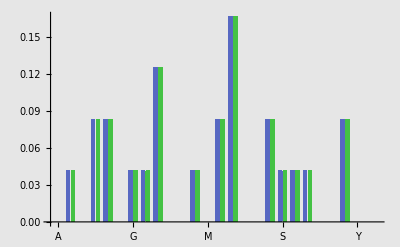

```mathematica
BEZGrafyRelCetnosti[OT,ST]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalýza transpozice

Kryptoanalýzu transpoziční šifry provádíme na základě bigramové analýzy. V šifrovém textu hledáme bigramy, avšak mezi jednotlivými znaky bigramů bývá zpravidla několik (někdy mnoho) dalších znaků. Pro angličtinu je typické hledat bigramy s největší četností, což jsou: TH, HE, AN, RE, ER, IN, ON, AT, ND, ST, ES, EN, OF, TE a ze vzdáleností znaků bigramů se snažíme stanovit parametry transpozice, které byly použity. Pro šifrový text TDIRHIEOESDNGBIOOUNXLROX vidíme ihned bigramy TH a HE z čehož usoudíme, že měla matice 4 řádky:

```mathematica
Transpozice["TDIRHIEOESDNGBIOOUNXLROX",4]
```

THEGOLDISBURIEDINORONOXX

Další možností je faktorizovat délku textu a tím zjistit všechny dělitele délky textu a postupně je zkusit.

```mathematica
FactorInteger[StringLength["TDIRHIEOESDNGBIOOUNXLROX"]]/.{x_Integer,y_Integer}->HoldForm[x^y]
```

{2^3,3^1}

Zde tento případ vidíme, že délka textu je 24 znaků. Z toho můžeme usoudit, že pro transpozice mohla být: 2*12, 3*8, 4*6, 6*4, 8*3, 12*2. Jiné kombinace neexistují. Pro náš případ byla použita transpozice 6*4.

Pokud text nebyl tak dlouhý, jak byl zadán předpis, musel být doplněn výplní (padding). Ze znalosti funkce, která transpozici provádí, víme, že tato funkce doplňuje na konec textu písmena X, dokud nezarovná text na potřebnou délku a to je skutečnost, kterou můžeme využít k prolomení transpozice, protože vzdálenost této výplně (zvláště v případě, že bylo doplněno více znaků X) udává transpoziční konstantu, která byla použita při šifrování. Délka textu / tato konstanta udává detranspoziční konstantu.

Pro náš text vidíme, že vzdálenost paddingu X je 4 znaky, z čehož rovnou plyne konstanta pro detranspozici.

Upozornění: Pokud byla transpozice použita vícenásobně, je její kryptoanalýza značně obtížnější!!

```mathematica
Transpozice[Transpozice["THEGOLDISBURIEDINORONO",4],3]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Ukol 3: Kryptoanalýza transpozice

Napište kus anglického textu o délce 30-50 znaků a náhodně zvolte transpoziční konstantu. Proveďte nad tímto textem transpozici s vámi zvolenou konstantou a výsledný šifrový text pošlete sousedovi.

```mathematica
OT="THISISSOMERANDOMTEXTTRYTOFINDTHEREALSTRING"
```

THISISSOMERANDOMTEXTTRYTOFINDTHEREALSTRING

```mathematica
Transpozice[OT,5]
```

TSRMTFHLNHSATRIESGIONEYNRTXSMDXTDERXIEOTOTAIX

Až obdržíte text od souseda, přiřaďte ho do této proměnné:

```mathematica
ST="SEQPIMAMCYVNEPBUASENAOTISSOOANARATMESEDNBRTNINEELIRDGSESACIDDEOID"
```

SEQPIMAMCYVNEPBUASENAOTISSOOANARATMESEDNBRTNINEELIRDGSESACIDDEOID

Nyní se snažte zjistit, jakou transpozici váš soused použil. Využijte metod popsaných na minulém slajdu. Pro jednoduchost faktorizaci opakujeme nyní pro proměnnou šifrového textu:

```mathematica
FactorInteger[StringLength[ST]]/.{x_Integer,y_Integer}->HoldForm[x^y]
```

{2^3,3^1}

```mathematica
Transpozice[ST,13]
```

SPONGEBOBSQUAREPANTSISANAMERICANANIMATEDCOMEDYTELEVISIONSERIESDDD

Postup: Podíval jsem se na zašifrovaný text a na všechny možné kombinace TH, HE a AN. S tím, že TH a HE jsem žádné nenašel, potom jsem vyzkoušel AN s tím, že sem zvolil za A první A ve stringu a pak k němu hledal N. První N se nachází ve vzdálenosti 6 což jsem zkusil a nevyšlo, další N v pořadí se nachází na pozici 13 což jsem zkusil a to dalo smysluplný výsledek.